```mathematica
NewtonRaphson [p0_,cifras_] :=
Method[{}, a = N[p0];
e=10^(-N[cifras]);
n = 0;
b = a - N [f[a]/f'[a]];
error = Abs[(b-a)/b];
vector = {{n, a, b, f[b],error}};
While[(((f(b) > e ) || (error ≥ 5*e)) && n≤ 40), a=b;
b = a -f[a]/f'[a];
error = Abs[(b-a)/b];
n = n+1 ; vector = Append[vector, {n,a,b,f[b],error}];
];
Print[NumberForm[TableForm[vector,TableHeadings->{None, {"n","x(n-1)","xn","f(xn)","er"}}],16]];
];
```

traza una tangente que pasa por x0 y f(x0), donde la tangente corta es el nuevo punto aproximado a la raiz

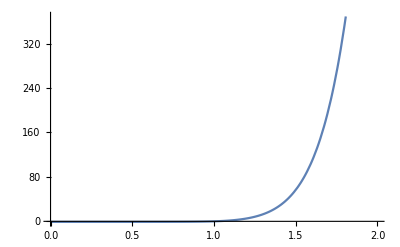

```mathematica
f[x_]=x^10-1;
Plot[f[x],{x,0,2}]
```

```mathematica
NewtonRaphson[0.5,4]
```

n | x(n-1) | xn | f(xn) | er
0 | 0.5 | 51.65000000000001 | 1.35114904483914×10^17 | 0.990319457889642
1 | 51.65000000000001 | 46.485 | 4.711165412971161×10^16 | 0.1111111111111111
2 | 46.485 | 41.83650000000001 | 1.642681807247857×10^16 | 0.1111111111111111
3 | 41.83650000000001 | 37.65285000000001 | 5.727677301318319×10^15 | 0.1111111111111111
4 | 37.65285000000001 | 33.88756500000001 | 1.99711758681985×10^15 | 0.111111111111111
5 | 33.88756500000001 | 30.49880850000001 | 6.963518448686211×10^14 | 0.1111111111111111
6 | 30.49880850000001 | 27.44892765000001 | 2.428028750295477×10^14 | 0.111111111111111
7 | 27.44892765000001 | 24.70403488500002 | 8.46601277170977×10^13 | 0.1111111111111106
8 | 24.70403488500002 | 22.23363139650005 | 2.951916127106414×10^13 | 0.1111111111111096
9 | 22.23363139650005 | 20.01026825685012 | 1.029269510505472×10^13 | 0.1111111111111069
10 | 20.01026825685012 | 18.0092414311653 | 3.58884087365512×10^12 | 0.1111111111110991
11 | 18.0092414311653 | 16.20831728804928 | 1.251351437592925×10^12 | 0.1111111111110767
12 | 16.20831728804928 | 14.58748555924565 | 4.363192672765299×10^11 | 0.1111111111110124
13 | 14.58748555924565 | 13.12873700332442 | 1.521351214992914×10^11 | 0.1111111111108282
14 | 13.12873700332442 | 11.81586330300061 | 5.304623684853301×10^10 | 0.1111111111102996
15 | 11.81586330300061 | 10.63427697272282 | 1.849607911725772×10^10 | 0.1111111111087838
16 | 10.63427697272282 | 9.57084927550804 | 6.4491840143077×10^9 | 0.1111111111044364
17 | 9.57084927550804 | 8.61376434810564 | 2.248691421762763×10^9 | 0.1111111110919682
18 | 8.61376434810564 | 7.752387913678128 | 7.840702169425907×10^8 | 0.1111111110562095
19 | 7.752387913678128 | 6.977149123299052 | 2.733883799085098×10^8 | 0.1111111109536549
20 | 6.977149123299052 | 6.279434213521248 | 9.53246335840643×10^7 | 0.1111111106595309
21 | 6.279434213521248 | 5.651490798756543 | 3.323764427729456×10^7 | 0.1111111098159916

Method[{},Null]

```mathematica
NewtonRaphson[1,10]
```

n | x(n-1) | xn | f(xn) | er
0 | 1. | 1. | 0. | 0.

Method[{},Null]

```mathematica
f[x_]:=E^(1-x/3)*x/3-0.25;
f'[x]
```

1/3 ⅇ^(1-x/3)-1/9 ⅇ^(1-x/3) x

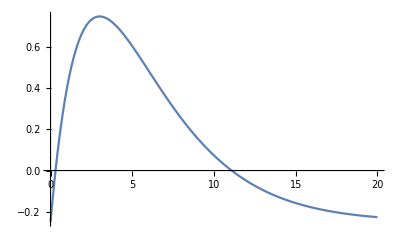

```mathematica
Plot[f[x],{x,0,20}]
```

```mathematica
NewtonRaphson[11,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 11. | 11.07727359823909 | 0.00003828433225211425 | 0.006975867983560127
1 | 11.07727359823909 | 11.07790354509074 | 2.526545195280505×10^-9 | 0.00005686516849362809
2 | 11.07790354509074 | 11.07790358666909 | 5.551115123125783×10^-17 | 3.753268617160091×10^-9

Method[{},Null]

```mathematica
f[x_]:=(1/2)+(1/4)*x^2-x*Sin[x]-(1/2)Cos[2x];
```

```mathematica
NewtonRaphson[Pi/2,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 1.570796326794897 | 1.785398163397448 | 0.007116977785672773 | 0.1201983070231148
1 | 1.785398163397448 | 1.844561629601787 | 0.001638543562279882 | 0.03207454023485831
2 | 1.844561629601787 | 1.870834417688862 | 0.0003963293781463761 | 0.01404335297590439
3 | 1.870834417688862 | 1.883346426927206 | 0.0000976011746864902 | 0.006643498540392301
4 | 1.883346426927206 | 1.889463764182278 | 0.00002422483102826334 | 0.003237604960219631
5 | 1.889463764182278 | 1.892489624534223 | 6.034836261381571×10^-6 | 0.001598878172285778
6 | 1.892489624534223 | 1.893994568355863 | 1.506071457546554×10^-6 | 0.0007945871898389529
7 | 1.893994568355863 | 1.894745069691104 | 3.761902405141626×10^-7 | 0.0003960962069496133
8 | 1.894745069691104 | 1.895119830909766 | 9.40067355070795×10^-8 | 0.0001977506712504379
9 | 1.895119830909766 | 1.895307089552274 | 2.349658911882102×10^-8 | 0.0000988012146105719
10 | 1.895307089552274 | 1.895400688432279 | 5.873510566800633×10^-9 | 0.00004938210721168448

Method[{},Null]

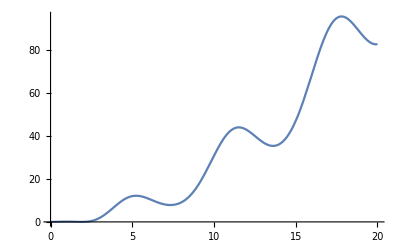

```mathematica
Plot[f[x],{x,0,20}]
```

```mathematica
NewtonRaphson[5Pi,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 15.70796326794897 | 13.08996938995747 | 36.54183996252717 | 0.2000000000000001
1 | 13.08996938995747 | 21.34757204878654 | 101.4799493188835 | 0.3868169476115414
2 | 21.34757204878654 | 17.47292729142397 | 94.4331539190304 | 0.2217513237901655
3 | 17.47292729142397 | 1.648679924132676 | 0.02980064850991648 | 9.59813189671487
4 | 1.648679924132676 | 1.798063088335893 | 0.005663214193764476 | 0.0830800460630505
5 | 1.798063088335893 | 1.849940057123163 | 0.001319265335816944 | 0.02804251337091633
6 | 1.849940057123163 | 1.873357313342177 | 0.0003203340064754645 | 0.01250015469672281
7 | 1.873357313342177 | 1.884572002167323 | 0.00007901398434650986 | 0.005950788196072771
8 | 1.884572002167323 | 1.890068173171549 | 0.0000196260749540933 | 0.00290792209627203
9 | 1.890068173171549 | 1.892789801826595 | 4.890957370440319×10^-6 | 0.001437892708645779
10 | 1.892789801826595 | 1.894144158281155 | 1.220816327585084×10^-6 | 0.0007150229028974245
11 | 1.894144158281155 | 1.894819740962411 | 3.049650676434368×10^-7 | 0.0003565419267338723
12 | 1.894819740962411 | 1.895157135744441 | 7.621147490866065×10^-8 | 0.0001780299773910654
13 | 1.895157135744441 | 1.895325734285068 | 1.904915003514418×10^-8 | 0.0000889549155472699
14 | 1.895325734285068 | 1.895410008879132 | 4.761822935961391×10^-9 | 0.00004446246124550278

Method[{},Null]

```mathematica
NewtonRaphson[10*Pi,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 31.41592653589793 | 47.1238898038469 | 555.1652475612766 | 0.3333333333333334
1 | 47.1238898038469 | 39.26990816987241 | 347.2615137476807 | 0.2
2 | 39.26990816987241 | 20.63495408493622 | 87.243366916534 | 0.903077080192776
3 | 20.63495408493622 | 14.08449084615 | 36.52549364747913 | 0.4650834247641109
4 | 14.08449084615 | 7.329538388391932 | 7.835332166225345 | 0.921606805205652
5 | 7.329538388391932 | 1921.54049146661 | 924804.976052246 | 0.996185592538413
6 | 1921.54049146661 | -6212.253387233748 | 9.65404907752552×10^6 | 1.309314571008227
7 | -6212.253387233748 | -4123.052940408521 | 4.245938385101907×10^6 | 0.5067120109833525
8 | -4123.052940408521 | 635.247836943754 | 100502.8373268835 | 7.490463564968555
9 | 635.247836943754 | 1166.40546624775 | 341020.9782852654 | 0.4553799211972965
10 | 1166.40546624775 | 910.572282382266 | 207713.8986711638 | 0.2809586771037725
11 | 910.572282382266 | 1506.290115134664 | 568726.686795523 | 0.3954867835663515
12 | 1506.290115134664 | 881.35794279295 | 193326.3499339998 | 0.7090560395488765
13 | 881.35794279295 | 538.2448537938887 | 72889.74867368348 | 0.6374665481343364
14 | 538.2448537938887 | 404.9426688272532 | 40866.29101933917 | 0.3291877967631553
15 | 404.9426688272532 | 335.1552319339658 | 27801.81339107107 | 0.2082242204323917
16 | 335.1552319339658 | 255.326284839633 | 16491.4928511734 | 0.312654637748997
17 | 255.326284839633 | 199.7093072680492 | 10166.88007343211 | 0.2784896624619246
18 | 199.7093072680492 | 21.9101603855625 | 118.2478017411389 | 8.11491763427007
19 | 21.9101603855625 | 18.27749556815234 | 93.7045934955001 | 0.1987506879082444
20 | 18.27749556815234 | 32.48006664593015 | 236.1035483691739 | 0.4372703797871496
21 | 32.48006664593015 | -488.6107779421886 | 60172.60827451788 | 1.066474314755646

Method[{},Null]

```mathematica
f[x_]:=0.653*x*(1-((1)/(ⅇ^(150/x))))-36;
```

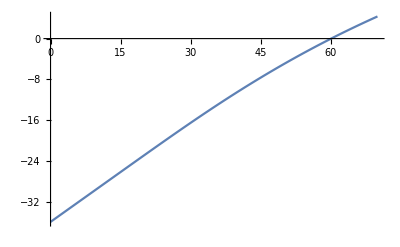

```mathematica
Plot[f[x],{x,0,70}]
```

```mathematica
NewtonRaphson[59,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 59. | 60.07066511384987 | -0.003217012107079142 | 0.01782342698920805
1 | 60.07066511384987 | 60.07758341508205 | -1.335395580781551×10^-7 | 0.0001151561171223652
2 | 60.07758341508205 | 60.07758370228755 | 0. | 4.780576904959958×10^-9

Method[{},Null]

```mathematica
f[x_]:=Tan[π*x]-6;
```

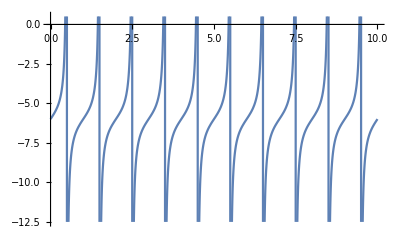

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
NewtonRaphson[0.4,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 0.4 | 0.4888264079717824 | 22.47599347689864 | 0.181713603281658
1 | 0.4888264079717824 | 0.4800143772536844 | 9.90600919700044 | 0.0183578474638916
2 | 0.4800143772536844 | 0.4676003353251227 | 3.790528574755307 | 0.02654840253681622
3 | 0.4676003353251227 | 0.4551428517295485 | 1.049042803562829 | 0.02737049159013627
4 | 0.4551428517295485 | 0.4485552160272789 | 0.1334414568116715 | 0.01468634287795014
5 | 0.4485552160272789 | 0.4474553527364219 | 0.002768827326400825 | 0.002458040303084303
6 | 0.4474553527364219 | 0.4474315539744564 | 1.242095696518675×10^-6 | 0.00005318972646032847
7 | 0.4474315539744564 | 0.4474315432887487 | 2.495781359357352×10^-13 | 2.388232961405494×10^-8

Method[{},Null]

```mathematica
f[x_]:=4x^2-E^x +E^(-x);
```

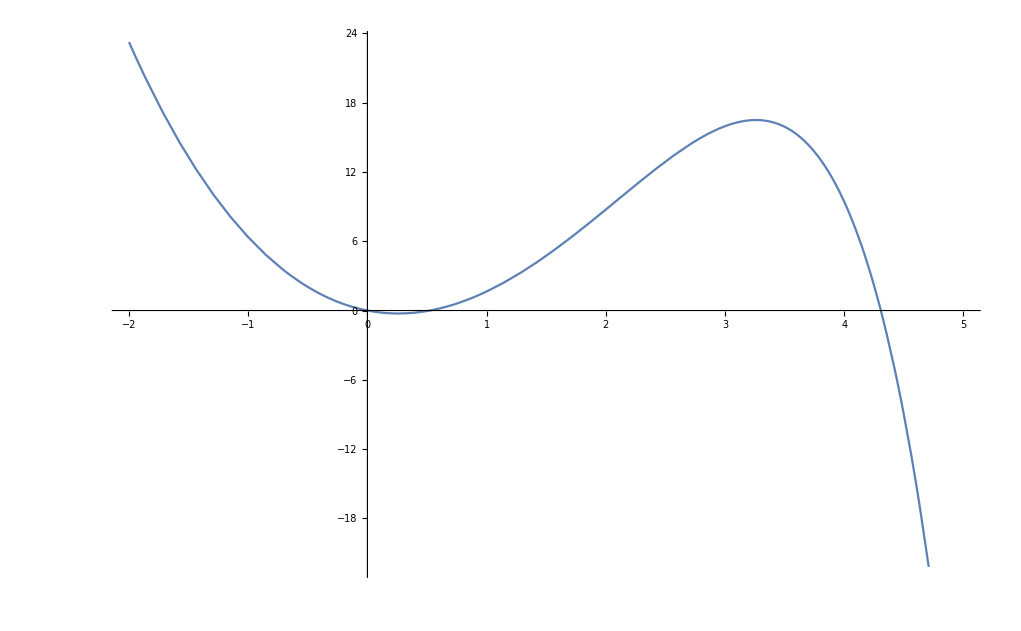

```mathematica
Plot[f[x],{x,-2,5}]
```

```mathematica
NewtonRaphson[0.4,5]
```

n | x(n-1) | xn | f(xn) | er
0 | 0.4 | 0.5748843593553352 | 0.1078130203725574 | 0.304207892438485
1 | 0.5748843593553352 | 0.5271663902119347 | 0.007767812029533361 | 0.0905178517246076
2 | 0.5271663902119347 | 0.5231477198930211 | 0.00005571011458715969 | 0.007681712384668991
3 | 0.5231477198930211 | 0.523118478794651 | 2.952178834725316×10^-9 | 0.00005589765904939778
4 | 0.523118478794651 | 0.5231184772449486 | 1.110223024625157×10^-16 | 2.962431160176799×10^-9

Method[{},Null]